```mathematica
semiMajorAxis=149598261;
period = 24 * 365.256363004;
ecc=0.01671123;
μ = 1.32712440018*10^11 ;(* for sun in km3/s2 *)
velocity=(2π*semiMajorAxis)/period * (1 - 1/4*ecc^2-3/64*ecc^4-5/256*ecc^6-175/16384*ecc^8);
distance = 149600000;
instVelocity=√(μ*(2/distance-1/semiMajorAxis))
```

29.7843

```mathematica
√(1.327*10^20*(2/(distance*1000)-1/(semiMajorAxis*1000)))
```

29782.9

```mathematica
PlanetData["Earth", EntityProperty["Planet", "DistanceFromSun", {"Date"->#}]]&/@DateObject[{2015,1,1}]
```

DateObject[Missing[UnknownEntity,{Planet,Earth}]]

```mathematica
speedTable=Table[.001*√(1.327*10^20*(2/((distanceTable[[i,2]]*1.496*10^8)*1000)-1/(semiMajorAxis*1000))), {i,1,366}]
distanceTable[[All,2]]
```

{30.2842,30.2845,30.2845,30.2845,30.2845,30.2839,30.2836,30.283,30.2821,30.2812,30.28,30.2788,30.2772,30.2757,30.2739,30.2721,30.27,30.2679,30.2654,30.263,30.2603,30.2576,30.2548,30.2515,30.2485,30.2452,30.2415,30.2379,30.2343,30.2303,30.2261,30.2222,30.2176,30.2134,30.2089,30.204,30.1992,30.1944,30.1892,30.1841,30.1787,30.1732,30.1675,30.1621,30.156,30.1503,30.1443,30.1383,30.1319,30.1256,30.1193,30.1126,30.106,30.0991,30.0925,30.0856,30.0786,30.0714,30.0642,30.057,30.0498,30.0423,30.0348,30.0272,30.0197,30.0119,30.0041,29.9963,29.9885,29.9804,29.9726,29.9645,29.9565,29.9484,29.94,29.9319,29.9235,29.9154,29.9071,29.8987,29.8903,29.8817,29.8733,29.8649,29.8563,29.8479,29.8393,29.8306,29.8223,29.8136,29.805,29.7966,29.788,29.7793,29.7707,29.7624,29.7537,29.7451,29.7368,29.7282,29.7198,29.7115,29.7029,29.6946,29.6863,29.678,29.6697,29.6613,29.653,29.645,29.6367,29.6287,29.6207,29.6127,29.6047,29.597,29.5891,29.5814,29.5737,29.566,29.5586,29.5512,29.5438,29.5364,29.529,29.522,29.5149,29.5078,29.5007,29.4939,29.4871,29.4807,29.4739,29.4674,29.4609,29.4547,29.4485,29.4424,29.4365,29.4303,29.4247,29.4188,29.4132,29.4079,29.4023,29.397,29.392,29.387,29.382,29.3773,29.3726,29.3679,29.3635,29.3591,29.355,29.3509,29.3468,29.343,29.3395,29.3356,29.3324,29.3289,29.3257,29.3227,29.3198,29.3169,29.3142,29.3116,29.3093,29.3072,29.3049,29.3028,29.301,29.2993,29.2978,29.2964,29.2949,29.2937,29.2928,29.292,29.2911,29.2905,29.2902,29.2896,29.2896,29.2896,29.2896,29.2899,29.2902,29.2908,29.2914,29.2923,29.2931,29.294,29.2955,29.2966,29.2981,29.2999,29.3016,29.3034,29.3054,29.3075,29.3098,29.3125,29.3148,29.3175,29.3204,29.3233,29.3266,29.3298,29.333,29.3365,29.3403,29.3439,29.348,29.3518,29.3559,29.3603,29.3647,29.3691,29.3738,29.3785,29.3832,29.3882,29.3932,29.3985,29.4038,29.4091,29.4147,29.4203,29.4262,29.4318,29.4379,29.4438,29.45,29.4562,29.4627,29.4689,29.4756,29.4821,29.4889,29.4957,29.5025,29.5096,29.5166,29.5237,29.5308,29.5382,29.5456,29.553,29.5604,29.5681,29.5757,29.5834,29.5911,29.5988,29.6068,29.6148,29.6228,29.6308,29.6388,29.6471,29.6551,29.6634,29.6717,29.68,29.6884,29.6967,29.705,29.7133,29.7219,29.7302,29.7389,29.7475,29.7558,29.7645,29.7731,29.7814,29.7901,29.7987,29.8073,29.8157,29.8243,29.833,29.8413,29.85,29.8584,29.867,29.8754,29.8837,29.8921,29.9008,29.9092,29.9172,29.9256,29.934,29.9421,29.9502,29.9586,29.9666,29.9744,29.9825,29.9903,29.9984,30.0062,30.0137,30.0215,30.029,30.0366,30.0441,30.0516,30.0588,30.066,30.0732,30.0801,30.0874,30.094,30.1009,30.1075,30.1142,30.1208,30.1271,30.1334,30.1398,30.1458,30.1518,30.1576,30.1633,30.169,30.1745,30.1799,30.1853,30.1905,30.1956,30.2004,30.2053,30.2098,30.2143,30.2189,30.2231,30.2273,30.2312,30.2352,30.2388,30.2424,30.2461,30.2494,30.2524,30.2554,30.2585,30.2612,30.2636,30.266,30.2685,30.2706,30.2724,30.2745,30.276,30.2775,30.2791,30.2803,30.2815,30.2824,30.283,30.2836,30.2842}

{0.98331,0.9833,0.9833,0.9833,0.9833,0.98332,0.98333,0.98335,0.98338,0.98341,0.98345,0.98349,0.98354,0.98359,0.98365,0.98371,0.98378,0.98385,0.98393,0.98401,0.9841,0.98419,0.98428,0.98439,0.98449,0.9846,0.98472,0.98484,0.98496,0.98509,0.98523,0.98536,0.98551,0.98565,0.9858,0.98596,0.98612,0.98628,0.98645,0.98662,0.9868,0.98698,0.98717,0.98735,0.98755,0.98774,0.98794,0.98814,0.98835,0.98856,0.98877,0.98899,0.98921,0.98944,0.98966,0.98989,0.99012,0.99036,0.9906,0.99084,0.99108,0.99133,0.99158,0.99183,0.99208,0.99234,0.9926,0.99286,0.99312,0.99339,0.99365,0.99392,0.99419,0.99446,0.99474,0.99501,0.99529,0.99556,0.99584,0.99612,0.9964,0.99669,0.99697,0.99725,0.99754,0.99782,0.99811,0.9984,0.99868,0.99897,0.99926,0.99954,0.99983,1.00012,1.00041,1.00069,1.00098,1.00127,1.00155,1.00184,1.00212,1.0024,1.00269,1.00297,1.00325,1.00353,1.00381,1.00409,1.00437,1.00464,1.00492,1.00519,1.00546,1.00573,1.006,1.00626,1.00653,1.00679,1.00705,1.00731,1.00756,1.00781,1.00806,1.00831,1.00856,1.0088,1.00904,1.00928,1.00952,1.00975,1.00998,1.0102,1.01043,1.01065,1.01087,1.01108,1.01129,1.0115,1.0117,1.01191,1.0121,1.0123,1.01249,1.01267,1.01286,1.01304,1.01321,1.01338,1.01355,1.01371,1.01387,1.01403,1.01418,1.01433,1.01447,1.01461,1.01475,1.01488,1.015,1.01513,1.01524,1.01536,1.01547,1.01557,1.01567,1.01577,1.01586,1.01595,1.01603,1.0161,1.01618,1.01625,1.01631,1.01637,1.01642,1.01647,1.01652,1.01656,1.01659,1.01662,1.01665,1.01667,1.01668,1.0167,1.0167,1.0167,1.0167,1.01669,1.01668,1.01666,1.01664,1.01661,1.01658,1.01655,1.0165,1.01646,1.01641,1.01635,1.01629,1.01623,1.01616,1.01609,1.01601,1.01592,1.01584,1.01575,1.01565,1.01555,1.01544,1.01533,1.01522,1.0151,1.01497,1.01485,1.01471,1.01458,1.01444,1.01429,1.01414,1.01399,1.01383,1.01367,1.01351,1.01334,1.01317,1.01299,1.01281,1.01263,1.01244,1.01225,1.01205,1.01186,1.01165,1.01145,1.01124,1.01103,1.01081,1.0106,1.01037,1.01015,1.00992,1.00969,1.00946,1.00922,1.00898,1.00874,1.0085,1.00825,1.008,1.00775,1.0075,1.00724,1.00698,1.00672,1.00646,1.0062,1.00593,1.00566,1.00539,1.00512,1.00485,1.00457,1.0043,1.00402,1.00374,1.00346,1.00318,1.0029,1.00262,1.00234,1.00205,1.00177,1.00148,1.00119,1.00091,1.00062,1.00033,1.00005,0.99976,0.99947,0.99918,0.9989,0.99861,0.99832,0.99804,0.99775,0.99747,0.99718,0.9969,0.99662,0.99634,0.99605,0.99577,0.9955,0.99522,0.99494,0.99467,0.9944,0.99412,0.99385,0.99359,0.99332,0.99306,0.99279,0.99253,0.99228,0.99202,0.99177,0.99152,0.99127,0.99102,0.99078,0.99054,0.9903,0.99007,0.98983,0.98961,0.98938,0.98916,0.98894,0.98872,0.98851,0.9883,0.98809,0.98789,0.98769,0.9875,0.98731,0.98712,0.98694,0.98676,0.98658,0.98641,0.98624,0.98608,0.98592,0.98577,0.98562,0.98547,0.98533,0.98519,0.98506,0.98493,0.98481,0.98469,0.98457,0.98446,0.98436,0.98426,0.98416,0.98407,0.98399,0.98391,0.98383,0.98376,0.9837,0.98363,0.98358,0.98353,0.98348,0.98344,0.9834,0.98337,0.98335,0.98333,0.98331}

```mathematica
ListPlot[speedTable, Axes->False,Frame->True, FrameLabel->{"Day of the Year (January 1, 2015 = 1)","???"}, PlotStyle->Directive[RGBColor[.6, .4,1], PointSize[Small]],Joined->True, BaseStyle->{FontFamily->"Helvetica Neue",FontSize->16}]
```

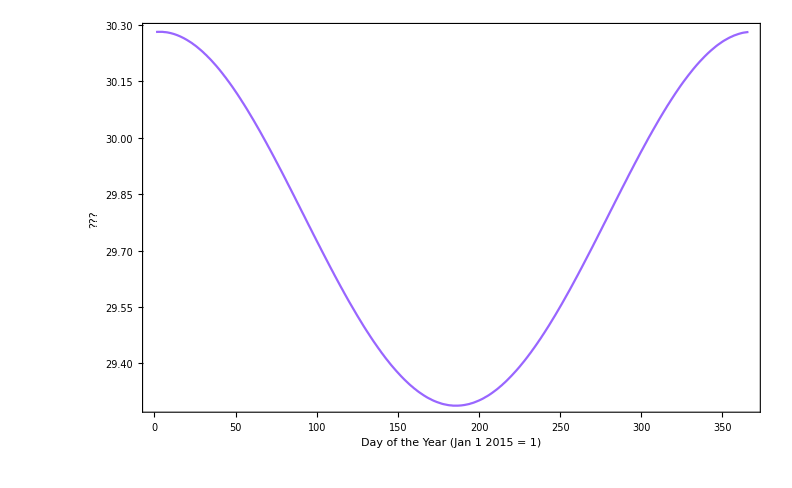

```mathematica
distanceTable = Import["Desktop/puzzles-starting-2015/raw-puzzle-2-earth-speed/distToSun2015.csv"];
```

{{1,0.98331},{2,0.9833},{3,0.9833},{4,0.9833},{5,0.9833},{6,0.98332},{7,0.98333},{8,0.98335},{9,0.98338},{10,0.98341},{11,0.98345},{12,0.98349},{13,0.98354},{14,0.98359},{15,0.98365},{16,0.98371},{17,0.98378},{18,0.98385},{19,0.98393},{20,0.98401},{21,0.9841},{22,0.98419},{23,0.98428},{24,0.98439},{25,0.98449},{26,0.9846},{27,0.98472},{28,0.98484},{29,0.98496},{30,0.98509},{31,0.98523},{32,0.98536},{33,0.98551},{34,0.98565},{35,0.9858},{36,0.98596},{37,0.98612},{38,0.98628},{39,0.98645},{40,0.98662},{41,0.9868},{42,0.98698},{43,0.98717},{44,0.98735},{45,0.98755},{46,0.98774},{47,0.98794},{48,0.98814},{49,0.98835},{50,0.98856},{51,0.98877},{52,0.98899},{53,0.98921},{54,0.98944},{55,0.98966},{56,0.98989},{57,0.99012},{58,0.99036},{59,0.9906},{60,0.99084},{61,0.99108},{62,0.99133},{63,0.99158},{64,0.99183},{65,0.99208},{66,0.99234},{67,0.9926},{68,0.99286},{69,0.99312},{70,0.99339},{71,0.99365},{72,0.99392},{73,0.99419},{74,0.99446},{75,0.99474},{76,0.99501},{77,0.99529},{78,0.99556},{79,0.99584},{80,0.99612},{81,0.9964},{82,0.99669},{83,0.99697},{84,0.99725},{85,0.99754},{86,0.99782},{87,0.99811},{88,0.9984},{89,0.99868},{90,0.99897},{91,0.99926},{92,0.99954},{93,0.99983},{94,1.00012},{95,1.00041},{96,1.00069},{97,1.00098},{98,1.00127},{99,1.00155},{100,1.00184},{101,1.00212},{102,1.0024},{103,1.00269},{104,1.00297},{105,1.00325},{106,1.00353},{107,1.00381},{108,1.00409},{109,1.00437},{110,1.00464},{111,1.00492},{112,1.00519},{113,1.00546},{114,1.00573},{115,1.006},{116,1.00626},{117,1.00653},{118,1.00679},{119,1.00705},{120,1.00731},{121,1.00756},{122,1.00781},{123,1.00806},{124,1.00831},{125,1.00856},{126,1.0088},{127,1.00904},{128,1.00928},{129,1.00952},{130,1.00975},{131,1.00998},{132,1.0102},{133,1.01043},{134,1.01065},{135,1.01087},{136,1.01108},{137,1.01129},{138,1.0115},{139,1.0117},{140,1.01191},{141,1.0121},{142,1.0123},{143,1.01249},{144,1.01267},{145,1.01286},{146,1.01304},{147,1.01321},{148,1.01338},{149,1.01355},{150,1.01371},{151,1.01387},{152,1.01403},{153,1.01418},{154,1.01433},{155,1.01447},{156,1.01461},{157,1.01475},{158,1.01488},{159,1.015},{160,1.01513},{161,1.01524},{162,1.01536},{163,1.01547},{164,1.01557},{165,1.01567},{166,1.01577},{167,1.01586},{168,1.01595},{169,1.01603},{170,1.0161},{171,1.01618},{172,1.01625},{173,1.01631},{174,1.01637},{175,1.01642},{176,1.01647},{177,1.01652},{178,1.01656},{179,1.01659},{180,1.01662},{181,1.01665},{182,1.01667},{183,1.01668},{184,1.0167},{185,1.0167},{186,1.0167},{187,1.0167},{188,1.01669},{189,1.01668},{190,1.01666},{191,1.01664},{192,1.01661},{193,1.01658},{194,1.01655},{195,1.0165},{196,1.01646},{197,1.01641},{198,1.01635},{199,1.01629},{200,1.01623},{201,1.01616},{202,1.01609},{203,1.01601},{204,1.01592},{205,1.01584},{206,1.01575},{207,1.01565},{208,1.01555},{209,1.01544},{210,1.01533},{211,1.01522},{212,1.0151},{213,1.01497},{214,1.01485},{215,1.01471},{216,1.01458},{217,1.01444},{218,1.01429},{219,1.01414},{220,1.01399},{221,1.01383},{222,1.01367},{223,1.01351},{224,1.01334},{225,1.01317},{226,1.01299},{227,1.01281},{228,1.01263},{229,1.01244},{230,1.01225},{231,1.01205},{232,1.01186},{233,1.01165},{234,1.01145},{235,1.01124},{236,1.01103},{237,1.01081},{238,1.0106},{239,1.01037},{240,1.01015},{241,1.00992},{242,1.00969},{243,1.00946},{244,1.00922},{245,1.00898},{246,1.00874},{247,1.0085},{248,1.00825},{249,1.008},{250,1.00775},{251,1.0075},{252,1.00724},{253,1.00698},{254,1.00672},{255,1.00646},{256,1.0062},{257,1.00593},{258,1.00566},{259,1.00539},{260,1.00512},{261,1.00485},{262,1.00457},{263,1.0043},{264,1.00402},{265,1.00374},{266,1.00346},{267,1.00318},{268,1.0029},{269,1.00262},{270,1.00234},{271,1.00205},{272,1.00177},{273,1.00148},{274,1.00119},{275,1.00091},{276,1.00062},{277,1.00033},{278,1.00005},{279,0.99976},{280,0.99947},{281,0.99918},{282,0.9989},{283,0.99861},{284,0.99832},{285,0.99804},{286,0.99775},{287,0.99747},{288,0.99718},{289,0.9969},{290,0.99662},{291,0.99634},{292,0.99605},{293,0.99577},{294,0.9955},{295,0.99522},{296,0.99494},{297,0.99467},{298,0.9944},{299,0.99412},{300,0.99385},{301,0.99359},{302,0.99332},{303,0.99306},{304,0.99279},{305,0.99253},{306,0.99228},{307,0.99202},{308,0.99177},{309,0.99152},{310,0.99127},{311,0.99102},{312,0.99078},{313,0.99054},{314,0.9903},{315,0.99007},{316,0.98983},{317,0.98961},{318,0.98938},{319,0.98916},{320,0.98894},{321,0.98872},{322,0.98851},{323,0.9883},{324,0.98809},{325,0.98789},{326,0.98769},{327,0.9875},{328,0.98731},{329,0.98712},{330,0.98694},{331,0.98676},{332,0.98658},{333,0.98641},{334,0.98624},{335,0.98608},{336,0.98592},{337,0.98577},{338,0.98562},{339,0.98547},{340,0.98533},{341,0.98519},{342,0.98506},{343,0.98493},{344,0.98481},{345,0.98469},{346,0.98457},{347,0.98446},{348,0.98436},{349,0.98426},{350,0.98416},{351,0.98407},{352,0.98399},{353,0.98391},{354,0.98383},{355,0.98376},{356,0.9837},{357,0.98363},{358,0.98358},{359,0.98353},{360,0.98348},{361,0.98344},{362,0.9834},{363,0.98337},{364,0.98335},{365,0.98333},{366,0.98331},{,}}

```mathematica
Directory[]
```

/Users/mcfink